# Heat partial differential equation

```mathematica
ClearAll["Global`*"];
```

## Initiation

Length of rod (cm) :

```mathematica
L=80;
```

Thermal conductivity (cal/(cm.s. °C)) :

```mathematica
K=0.95;
```

Density of the material (gm/cm^3) :

```mathematica
ρ=8.92;
```

Specific heat (cal/(gm. °C)) :

```mathematica
σ=0.092;
```

```mathematica
c=√(K/(σ ρ));
```

cm^2/s

```mathematica
c^2
```

1.15763

```mathematica
duration=500;
```

## Differential equation with initial conditions and boundary conditions

```mathematica
equ=D[U[x,t], t]==c^2 D[U[x,t], x,x];
```

Initial temperature distribution in the rod :

```mathematica
ic=U[x,0]==Sin[π/L x];
```

The ends of the rod maintained at zero temperature :

```mathematica
bc1=U[0,t]==0;
```

```mathematica
bc2=U[L,t]==0;
```

## NDSolve

```mathematica
sol=NDSolve[{equ,bc1,bc2,ic},
U[x,t],
{x,0,L},
{t,0,duration}];
```

```mathematica
U=U[x,t]/.sol;
```

```mathematica
Plot3D[U,
{x,0,L},
{t,0,duration},
PlotPoints->50,
PlotRange->All,
AxesLabel->{"x","t","U[x,t]"}]
```

-Graphics3D-

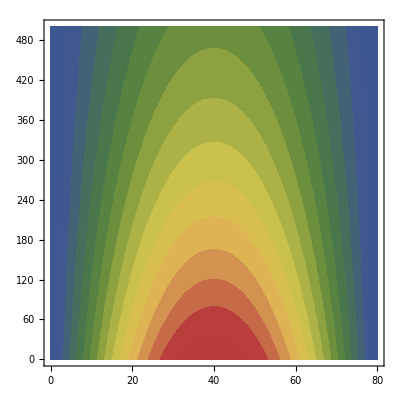

```mathematica
ContourPlot[U,
{x,0,L},
{t,0,duration},
PlotPoints->15,
Contours->15,
ContourLines->False,
AspectRatio->1,
ColorFunction->"DarkRainbow",
PlotRange->{{0,L},{0,duration}}]
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```